```mathematica
Clear[f, a, b, n, Nn, table, point, X, h, x,chebushevNodes,chebushevValues,error, errorS, errorc,chtable, Ni, Q1, Q2, Q3, Q4 ]
```

```mathematica
f[x_] = x*Cos[2*x];
a = -Pi/4;
b=Pi/3;
n = 5;
```

```mathematica
X = Table[a+(b-a)/n*j, {j, 0, n}];
```

```mathematica
Print[X];
```

{-π/4,-(2 π)/15,-π/60,π/10,(13 π)/60,π/3}

```mathematica
table = Round[Transpose[{X, f[X]}], 0.000001];
```

```mathematica
Print[table]
Grid[
	Prepend[table, {"x", "f[x]"}],
	   Frame -> All,
	   Alignment->Center]
```

{{-0.785398,0.},{-0.418879,-0.280285},{-0.05236,-0.052073},{0.314159,0.25416},{0.680678,0.141521},{1.0472,-0.523599}}

x | f[x]
-0.785398 | 0.
-0.418879 | -0.280285
-0.05236 | -0.052073
0.314159 | 0.25416
0.680678 | 0.141521
1.0472 | -0.523599

```mathematica
Clear[x];
Nn[x_]= InterpolatingPolynomial[table,x];
Expand[Nn];
```

{{0,-π/4},{1,-(2 π)/15},{2,-π/60},{3,π/10},{4,(13 π)/60},{5,π/3}}

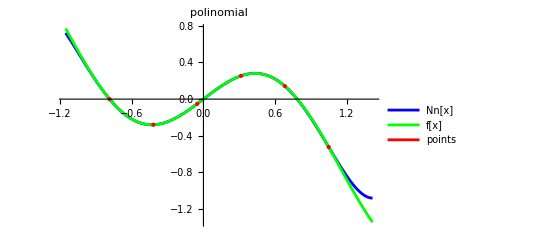

```mathematica
point = Transpose[{Range[0,n,1], X}];
Print[point]
h=(b-a)/n;
Plot[{Nn[x], f[x], t}, {x, a-h, b+h},
PlotLabel->"polinomial",
PlotStyle -> {Blue, Green, Red},
PlotLegends->{"Nn[x]", "f[x]", "points"},
Epilog->{
Red, PointSize[Large], Point[table]}]
```

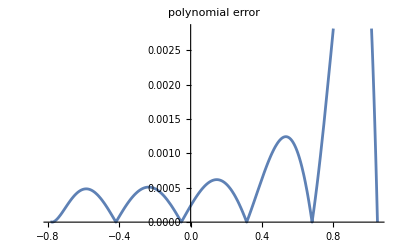

```mathematica
Plot[Abs[f[x]-Nn[x]], {x, a, b}, PlotLabel->"polynomial error"]
```

```mathematica
NMaximize[{Abs[f[x]-Nn[x]], a<=x<=b},x]
```

{0.00520799,{x→0.928858}}

```mathematica
Clear[x]
```

```mathematica
g[x_]=(a+b)/2+(b-a)/2*Cos[((2k+1)*Pi)/(2*(n+1))];
data = Table[{g[k],f[g[k]]}, {k, 0, n}]//N
Print[chebushevNodes]
```

{{1.01598,-0.452091},{0.77882,0.0102459},{0.368055,0.27276},{-0.106256,-0.103865},{-0.517021,-0.264379},{-0.754176,-0.0470633}}

chebushevNodes

```mathematica
Print[data]
Grid[
	Prepend[data, {"x", "f[x]"}],
	   Frame -> All,
	   Alignment->Center] //N
```

{{1.01598,-0.452091},{0.77882,0.0102459},{0.368055,0.27276},{-0.106256,-0.103865},{-0.517021,-0.264379},{-0.754176,-0.0470633}}

x | f[x]
1.01598 | -0.452091
0.77882 | 0.0102459
0.368055 | 0.27276
-0.106256 | -0.103865
-0.517021 | -0.264379
-0.754176 | -0.0470633

```mathematica
chebushevNn[x_]=InterpolatingPolynomial[data, x]
```

-0.452091+(-1.01598+x) (-0.22881+(0.754176+x) (-0.125769+(0.106256+x) (-1.40673+(-0.368055+x) (-0.00984518+0.534837 (0.517021+x)))))

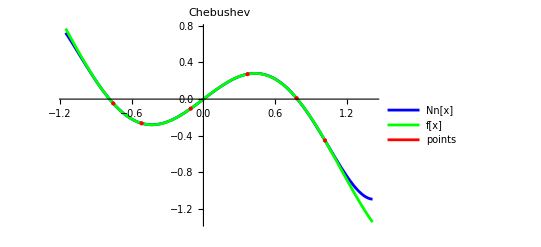

```mathematica
Plot[{chebushevNn[x], f[x],t}, {x, a-h, b+h},
PlotLabel->"Chebushev",
PlotStyle -> {Blue, Green, Red},
PlotLegends->{"Nn[x]", "f[x]", "points"},
Epilog->{
Red, PointSize[Large], Point[data]
}]
```

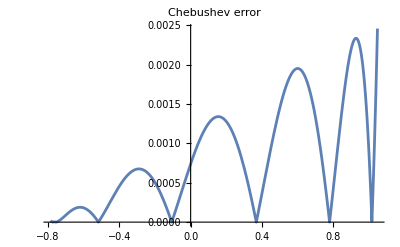

{0.00245619,{x→1.0472}}

```mathematica
Plot[ Abs[f[x]-chebushevNn[x]], {x, a, b}, PlotLabel->"Chebushev error"]
NMaximize[{Abs[f[x]-chebushevNn[x]], a<=x<=b},x]
```

InterpolatingFunction[…]

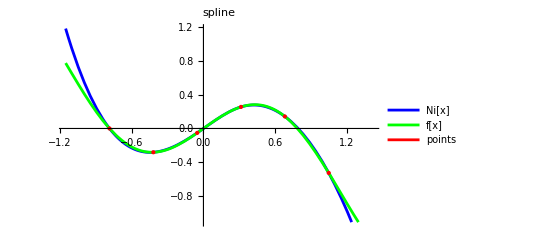

```mathematica
Ni = Interpolation[table, Method->"Spline"]
Plot[{Ni[x], f[x], t}, {x, a-h, b+h},
PlotLabel->"spline",
PlotStyle -> {Blue, Green, Red},
PlotLegends->{"Ni[x]", "f[x]", "points"},
Epilog->{
Red, PointSize[Large], Point[table]}
]
```

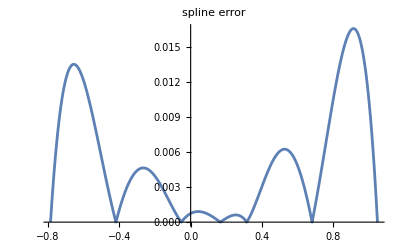

{0.0165606,{x→0.912864}}

```mathematica
Plot[Abs[f[x]-Ni[x]], {x, a, b}, PlotLabel->"spline error"]
NMaximize[{Abs[f[x]-Ni[x]], a<=x<=b},x]
```

```mathematica
Q1 = Fit[table, {1, x}, x] 
Q2 = Fit[table, {1, x, x^2}, x] 
Q3 = Fit[table, {1, x, x^2,x^3}, x]
 Q4 = Fit[table, {1, x, x^2,x^3,x^4}, x]
```

-0.0660357-0.0815663 x

0.0977044+0.0328439 x-0.437014 x^2

-0.0129136+0.834107 x+0.0648347 x^2-1.27794 x^3

0.0131444+0.912821 x-0.212343 x^2-1.45739 x^3+0.34272 x^4

-0.0660357-0.0815663 x

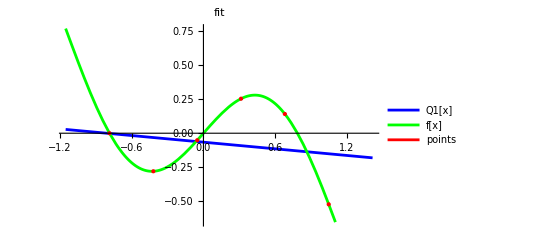

```mathematica
p[x_]=Q1
Plot[{p[x], f[x], t}, {x, a-h, b+h},
PlotLabel->"fit",
PlotStyle -> {Blue, Green, Red},
PlotLegends->{"Q1[x]", "f[x]", "points"},
Epilog->{
Red, PointSize[Large], Point[table]
}]
```

0.0977044+0.0328439 x-0.437014 x^2

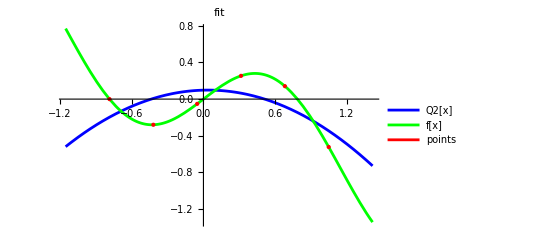

```mathematica
p[x_]=Q2
Plot[{p[x], f[x], t}, {x, a-h, b+h},
PlotLabel->"fit",
PlotStyle -> {Blue, Green, Red},
PlotLegends->{"Q2[x]", "f[x]", "points"},
Epilog->{
Red, PointSize[Large], Point[table]
}]
```

-0.0129136+0.834107 x+0.0648347 x^2-1.27794 x^3

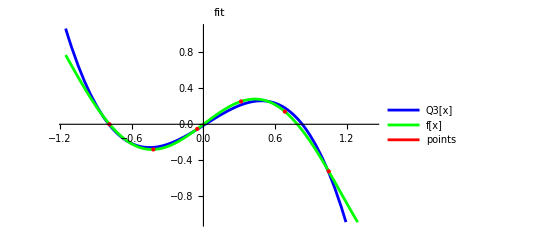

```mathematica
p[x_]=Q3
Plot[{p[x], f[x], t}, {x, a-h, b+h},
PlotLabel->"fit",
PlotStyle -> {Blue, Green, Red},
PlotLegends->{"Q3[x]", "f[x]", "points"},
Epilog->{
Red, PointSize[Large], Point[table]
}]
```

0.0131444+0.912821 x-0.212343 x^2-1.45739 x^3+0.34272 x^4

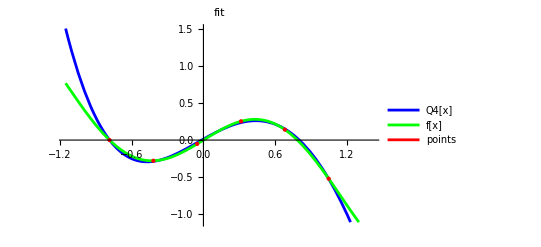

```mathematica
p[x_]=Q4
Plot[{p[x], f[x], t}, {x, a-h, b+h},
PlotLabel->"fit",
PlotStyle -> {Blue, Green, Red},
PlotLegends->{"Q4[x]", "f[x]", "points"},
Epilog->{
Red, PointSize[Large], Point[table]
}]
```